```mathematica
f[1][x_]:=InterpolatingPolynomial[{{1,5},{2,4},{3,1},{4,3},{5,2}},x];
f[i_][x_,1]:=f[i][x];
f[i_][x_,k_Integer]:=Nest[f[i][#]&,x,k];
x0= 1;
```

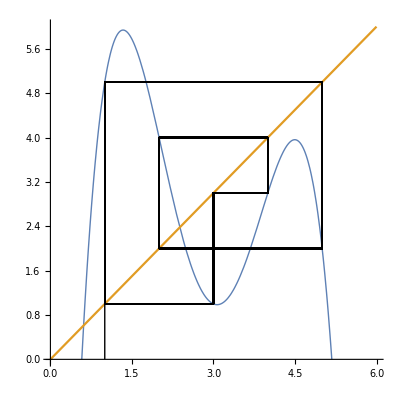

```mathematica
cobweb[ff_,x00_,lim_:False]:=Module[{pts1,pts2,pts,xs,x0},
x0=If[lim,Nest[ff[#]&,N@x00,2000],x00];
xs=NestList[ff[#]&,x0, 100];
pts1=Transpose@{xs,RotateLeft[xs]};
pts2=Transpose@{xs,xs};
pts=Rest@Most@Riffle[pts2,pts1];
Line@Most@pts
];
Plot[{f[1][x],x},{x,0,6}
,PlotRange->{0,6}
,AspectRatio->Automatic
,PlotStyle->{Thick,{}}
,Epilog->{cobweb[f[1],x0,True],Line@{{x0,0},{x0,f[1][x0]}}}]
```

```mathematica
f[1][x]
```

5+(-1+(-1+(7/6-5/8 (-4+x)) (-3+x)) (-2+x)) (-1+x)

```mathematica
NestList[f[1],x0, 5]
```

{1,5,2,4,3,1}